## Fermi Function -- Integration

#### Function Definitions

```mathematica
FFIntegrand[x_,m_,βμ_]:=x^(m-1)/(Exp[x-βμ]+1)
```

```mathematica
FFValue[m_,βμ_]:=Re[-PolyLog[m,-Exp[βμ]]]
```

```mathematica
FFValueFull[m_,βμ_]:=1/Factorial[m-1] NIntegrate[FFIntegrand[x,m,βμ],{x,0,Infinity}]
```

```mathematica
FFValuePartial[m_,βμ_]:=1/Factorial[m-1] NIntegrate[FFIntegrand[x,m,βμ],{x,0,2 βμ}]
```

```mathematica
FFErrorFull[m_,βμ_]:=Log[(FFValue[m,βμ]-FFValueFull[m,βμ])/FFValue[m,βμ]]
```

```mathematica
FFErrorPartial[m_,βμ_]:=Log[(FFValue[m,βμ]-FFValuePartial[m,βμ])/FFValue[m,βμ]]
```

#### Plots

```mathematica
Manipulate[Plot[FFIntegrand[x,m,βμ],{x,0,1000},PlotRange->All],{{βμ,500,"βμ"},-20,1000},{{m,3/2}}]
```

```mathematica
Manipulate[Plot[FFValue[m,βμ],{βμ,center-range,center+range}],{{center,0},-200,1000,100},{{range,0.1},{0.001,0.01,0.02,0.1,1}},{{m,3/2}}]
```

```mathematica
Manipulate[Plot[FFErrorFull[m,βμ],{βμ,-20,1000}],{{m,3/2}}]
```

```mathematica
Manipulate[Plot[FFErrorPartial[m,βμ],{βμ,-20,1000}],{{m,3/2}}]
```

```mathematica
Manipulate[Plot[FFValueFull[m,βμ]-FFValuePartial[m,βμ],{βμ,-20,1000}],{{m,3/2}}]
```

#### Polynomial Approximations

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,100,1000,1}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-18.4317+2.90365 x+0.0678718 x^2-0.000314877 x^3+1.75247×10^-6 x^4-8.19422×10^-9 x^5+3.03572×10^-11 x^6-8.72287×10^-14 x^7+1.90507×10^-16 x^8-3.04732×10^-19 x^9+3.25642×10^-22 x^10-1.58721×10^-25 x^11-1.26738×10^-28 x^12+2.85234×10^-31 x^13-1.48544×10^-34 x^14-1.47957×10^-37 x^15+3.1997×10^-40 x^16-2.69144×10^-43 x^17+1.28153×10^-46 x^18-3.4045×10^-50 x^19+3.95534×10^-54 x^20

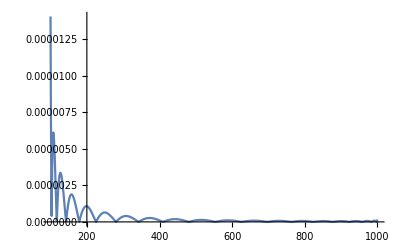

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,100,1000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,1000,10000,10}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-590.625+9.19557 x+0.0214442 x^2-9.93866×10^-6 x^3+5.5284×10^-9 x^4-2.58407×10^-12 x^5+9.57091×10^-16 x^6-2.74962×10^-19 x^7+6.00429×10^-23 x^8-9.6031×10^-27 x^9+1.02606×10^-30 x^10-4.99935×10^-35 x^11-3.99561×10^-39 x^12+8.98821×10^-43 x^13-4.67937×10^-47 x^14-4.6637×10^-51 x^15+1.0083×10^-54 x^16-8.48071×10^-59 x^17+4.03792×10^-63 x^18-1.07267×10^-67 x^19+1.2462×10^-72 x^20

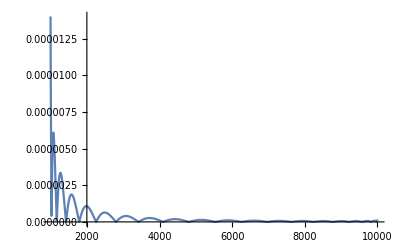

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,1000,10000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,10000,100000,100}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-18679.5+29.0793 x+0.00678121 x^2-3.14285×10^-7 x^3+1.74821×10^-11 x^4-8.17146×10^-16 x^5+3.02657×10^-20 x^6-8.69506×10^-25 x^7+1.89875×10^-29 x^8-3.03686×10^-34 x^9+3.2449×10^-39 x^10-1.58129×10^-44 x^11-1.26314×10^-49 x^12+2.84213×10^-54 x^13-1.4799×10^-59 x^14-1.47438×10^-64 x^15+3.18809×10^-69 x^16-2.68156×10^-74 x^17+1.27679×10^-79 x^18-3.39181×10^-85 x^19+3.94052×10^-91 x^20

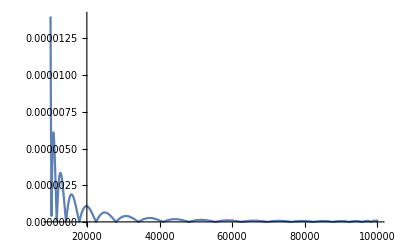

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,10000,100000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,100000,1000000,1000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-590694.+91.9565 x+0.00214441 x^2-9.93862×10^-9 x^3+5.52839×10^-14 x^4-2.58408×10^-19 x^5+9.57102×10^-25 x^6-2.74968×10^-30 x^7+6.00451×10^-36 x^8-9.60368×10^-42 x^9+1.02617×10^-47 x^10-5.0009×10^-54 x^11-3.99421×10^-60 x^12+8.98777×10^-66 x^13-4.68024×10^-72 x^14-4.66202×10^-78 x^15+1.00814×10^-83 x^16-8.47977×10^-90 x^17+4.03756×10^-96 x^18-1.07259×10^-102 x^19+1.24611×10^-109 x^20

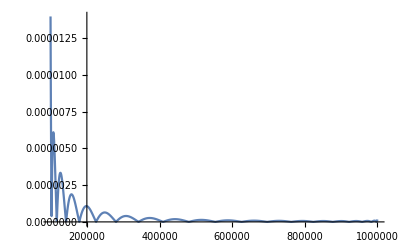

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,100000,1000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,1000000,10000000,10000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-1.86797×10^7+290.794 x+0.000678119 x^2-3.14282×10^-10 x^3+1.74819×10^-16 x^4-8.17131×10^-23 x^5+3.02649×10^-29 x^6-8.69475×10^-36 x^7+1.89865×10^-42 x^8-3.03663×10^-49 x^9+3.24448×10^-56 x^10-1.58072×10^-63 x^11-1.26373×10^-70 x^12+2.84255×10^-77 x^13-1.48005×10^-84 x^14-1.47444×10^-91 x^15+3.18821×10^-98 x^16-2.68164×10^-105 x^17+1.27682×10^-112 x^18-3.39188×10^-120 x^19+3.94059×10^-128 x^20

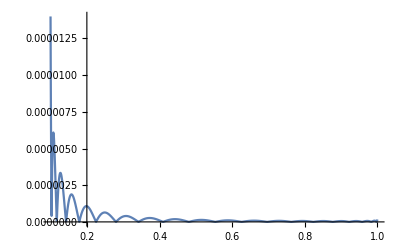

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,1000000,10000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,10000000,100000000,100000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-5.90697×10^8+919.567 x+0.000214441 x^2-9.93855×10^-12 x^3+5.52833×10^-19 x^4-2.58403×10^-26 x^5+9.57079×10^-34 x^6-2.74958×10^-41 x^7+6.00422×10^-49 x^8-9.60301×10^-57 x^9+1.02605×10^-64 x^10-4.99943×10^-73 x^11-3.99534×10^-81 x^12+8.98784×10^-89 x^13-4.67912×10^-97 x^14-4.66368×10^-105 x^15+1.00828×10^-112 x^16-8.48051×10^-121 x^17+4.03782×10^-129 x^18-1.07264×10^-137 x^19+1.24616×10^-146 x^20

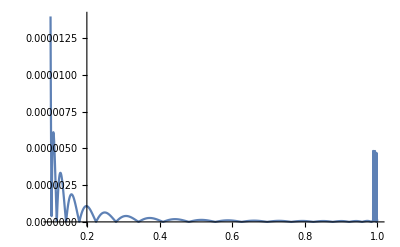

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,10000000,100000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,100000000,1000000000,1000000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-1.86797×10^10+2907.94 x+0.0000678119 x^2-3.14281×10^-13 x^3+1.74818×10^-21 x^4-8.17125×10^-30 x^5+3.02647×10^-38 x^6-8.69468×10^-47 x^7+1.89864×10^-55 x^8-3.03665×10^-64 x^9+3.2446×10^-73 x^10-1.58108×10^-82 x^11-1.26306×10^-91 x^12+2.84169×10^-100 x^13-1.47931×10^-109 x^14-1.47481×10^-118 x^15+3.18825×10^-127 x^16-2.68154×10^-136 x^17+1.27675×10^-145 x^18-3.39164×10^-155 x^19+3.94027×10^-165 x^20

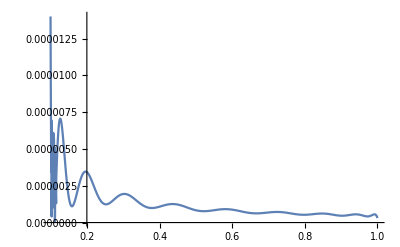

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,100000000,1000000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,1000000000,10000000000,10000000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-5.90704×10^11+9195.71 x+0.000021444 x^2-9.93845×10^-15 x^3+5.52824×10^-24 x^4-2.58398×10^-33 x^5+9.57056×10^-43 x^6-2.74951×10^-52 x^7+6.00407×10^-62 x^8-9.60281×10^-72 x^9+1.02605×10^-81 x^10-4.99986×10^-92 x^11-3.99439×10^-102 x^12+8.98692×10^-112 x^13-4.67906×10^-122 x^14-4.66266×10^-132 x^15+1.00813×10^-141 x^16-8.47938×10^-152 x^17+4.0373×10^-162 x^18-1.0725×10^-172 x^19+1.246×10^-183 x^20

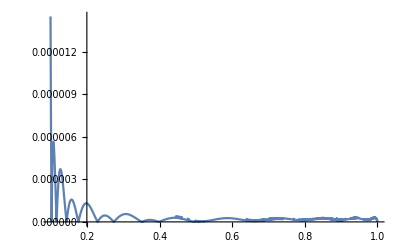

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,1000000000,10000000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,10000000000,100000000000,100000000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-1.86795×10^13+29079.3 x+6.78121×10^-6 x^2-3.14285×10^-16 x^3+1.74821×10^-26 x^4-8.17145×10^-37 x^5+3.02656×10^-47 x^6-8.695×10^-58 x^7+1.89872×10^-68 x^8-3.03679×10^-79 x^9+3.24476×10^-90 x^10-1.5811×10^-101 x^11-1.26333×10^-112 x^12+2.84224×10^-123 x^13-1.47987×10^-134 x^14-1.47449×10^-145 x^15+3.18821×10^-156 x^16-2.68163×10^-167 x^17+1.27682×10^-178 x^18-3.39187×10^-190 x^19+3.94058×10^-202 x^20

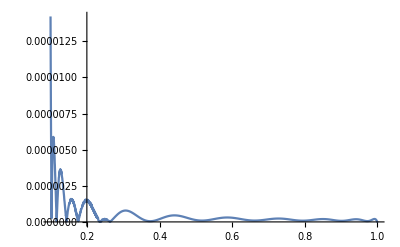

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,10000000000,100000000000},PlotRange->Full]
```

```mathematica
data=Table[{βμ,FFValue[3/2,βμ]},{βμ,100000000000,1000000000000,1000000000}];dataFit=Fit[data,{1,βμ,βμ^2,βμ^3,βμ^4,βμ^5,βμ^6,βμ^7,βμ^8,βμ^9,βμ^10,βμ^11,βμ^12,βμ^13,βμ^14,βμ^15,βμ^16,βμ^17,βμ^18,βμ^19,βμ^20},βμ];dataFit/.{βμ->x}
```

-5.90706×10^14+91957.1 x+2.1444×10^-6 x^2-9.93845×10^-18 x^3+5.52824×10^-29 x^4-2.58399×10^-40 x^5+9.57062×10^-52 x^6-2.74954×10^-63 x^7+6.00418×10^-75 x^8-9.60311×10^-87 x^9+1.0261×10^-98 x^10-5.00065×10^-111 x^11-3.99363×10^-123 x^12+8.98647×10^-135 x^13-4.67892×10^-147 x^14-4.66269×10^-159 x^15+1.00814×10^-170 x^16-8.4795×10^-183 x^17+4.03738×10^-195 x^18-1.07253×10^-207 x^19+1.24604×10^-220 x^20

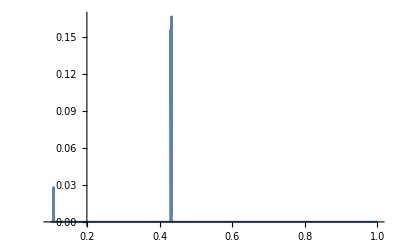

```mathematica
Plot[100Abs[(FFValue[3/2,βμ]-dataFit)/FFValue[3/2,βμ]],{βμ,100000000000,1000000000000},PlotRange->Full]
```

## Old

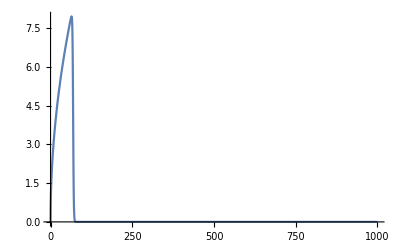

```mathematica
Plot[x^(3/2-1)/(( 10^30)^-1 Exp[x]+1),{x,0,1000},PlotRange->All]
```

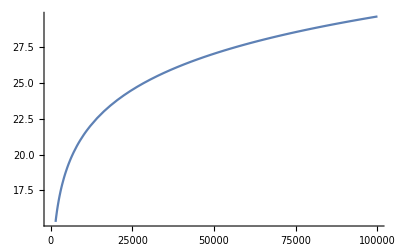

```mathematica
Plot[-PolyLog[3/2,-z],{z,0,100000}]
```

```mathematica
1/Factorial[m-1] Integrate[x^(m-1)/(z^-1 Exp[x]+1),{x,0,Infinity}]
```

ConditionalExpression[-(Gamma[m] PolyLog[m,-z])/((-1+m)!),Re[m]>0]

```mathematica
N[-PolyLog[3/2,-100]]
```

7.8891-2.89019×10^-17 ⅈ